```mathematica
Unprotect[npredictors];
SetDirectory[NotebookDirectory[]];
<<EQLab2`
```

```mathematica
SUPERARRAYNAME=(Join[SUPERARRAYNAME,{"BELIEF"}]//DeleteDuplicates);
ConstNamesSimRewardDriven={"PredictivePower"};
VarNamesSimRewardDriven={"beliefinα","affinity","bias","randomwalkh"};
```

```mathematica
(*measurements*)

UserMeasure[]:=RandomReal[]//Which[#<ProbabilityPlus,1,True,-1]&(*simple yes or no answer with equal probability*)
(*forecasts*)
predictivepower2[xrandom_,meas_]:=Which[meas==1,1-xrandom^6,meas==-1,xrandom^6]
predictivepower1[xrandom_,meas_]:=Which[meas==1,1-xrandom^2,meas==-1,xrandom^2]
predictivepower0[xrandom_,meas_]:=Which[meas==1,1-xrandom,meas==-1,xrandom]
predictivepowerm1[xrandom_,meas_]:=Which[meas==1,xrandom^(2) ,meas==-1,1-xrandom^(2) ]
predictivepowerm2[xrandom_,meas_]:=Which[meas==1,xrandom^(6) ,meas==-1,1-xrandom^(6) ]

predictivepower[xrandom_,meas_,g_]:=Which[(*should correspond to p(ν,di) in Eq 17*)
g==2,predictivepower2[xrandom,meas],
g==1,predictivepower1[xrandom,meas],
g==0,predictivepower0[xrandom,meas],
g==-1,predictivepowerm1[xrandom,meas],
g==-2,predictivepowerm2[xrandom,meas]
]
```

```mathematica
(*Random walk update of belief according to draft*)
RandomWalk[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,stepplus={},stepminus={}},


stepplus=Table[
Which[(*if ν1<h, proceed with random walk upwards*)
Random[]<=randomwalkh[[i]],1,
True,0
],
{i,1,beliefinα//Length}];

stepminus=Table[
Which[(*if ν2<h, proceed with random walk downwards*)
Random[]<=randomwalkh[[i]],-1,
True,0
],
{i,1,beliefinα//Length}];


(*update d_i according to random walk*)
beliefinα=beliefinα+stepplus+stepminus;


(*make sure that  -2 ≤ d_i ≤ 2, if not, force out of bounds values to wither +1 or -1*)
beliefinα=Table[
Which[
(beliefinα[[i]]<-2),beliefinα[[i]]=-1,
(beliefinα[[i]]>  2),beliefinα[[i]]=   1,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];

]
```

```mathematica
UpdateBelieveinαAffinity[]:=Module[
{rewards,maxreward,avgrewards,Largerewards,leadingexpert,changebelief={},beliefinαTEMP,it},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
Largerewards=(maxreward+avgrewards)/2;

leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;


changebelief=Table[
TrueQ[
!(Random[]<Exp[- affinity[[i]](1-rewards[[i]]/Largerewards)])
]
,{i,1,beliefinα//Length}];

beliefinα=Table[
Which[
changebelief[[i]],beliefinα[[i]]+Sign[  beliefinα[[leadingexpert]]-beliefinα[[i]]  ],
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];


];
```

```mathematica
UpdateBelieveinα[]:=Module[
{},
RandomWalk[];
UpdateBelieveinαAffinity[];
(*AppendTo[BeliefCurrent,beliefinα];*)
]
```

```mathematica
PrintBelieveinα[]:=Module[
{names=PLOTLEGENDS[[1,1;;npredictors]],output},
output=Table[names[[i]]<>"->"<>ToString[beliefinα[[i]]]<>"\n",{i,1,npredictors}]//StringJoin;
Print[Style["------ Current belief in theory α ---------",Red,Large]];
Print[Style["after ",Bold,Large],Style[BeliefCurrent//Length,Bold,Large,Blue],Style[" questions.",Bold,Large]];
Print[Style[output,Blue,Large]]
]
```

```mathematica
UserPredict[exp_,newquestion_]:=Module[
{forecasts={},tags},
tags=PredictivePower//Keys;
AppendTo[BeliefCurrent,beliefinα];
Which[
(exp//Length)>1,UpdateBelieveinα[];,
True,Nothing
];
forecasts=Table[RandomReal[{0.001,0.999}]//PredictivePower[i][#,newquestion[[2]]]&,{i,tags}];
forecasts
]
```

```mathematica
(*resolutions*)

UserResolve[exp_,newquestion_]:=Module[
{objectiveSij,objectiveSjavg,resolutions,wj,i},
objectiveSij=ObjectiveSurprisal[newquestion];
objectiveSjavg=Mean[objectiveSij];
wj=newquestion[[2]];

resolutions=Table[
Which[
Random[]<Exp[-bias[[i]]*(objectiveSij[[i]]/objectiveSjavg-1)] , wj,
True,-wj
],
{i,1,newquestion[[1]]//Length}
]

]

InitSimulationRewardDriven[INITbeliefinα_List,INITaffinity_List,INITbias_List,INITrandomwalkh_List]:=Module[
{},

(*variables*)
Clear["npredictors*"];
npredictorsUSER=INITbeliefinα//Length;

beliefinα=INITbeliefinα;
affinity=INITaffinity;
bias=INITbias;
randomwalkh=INITrandomwalkh;
BiasValues={};AffinityValues={};

BeliefCurrent={};
(*BELIEF={};*)

ProbabilityPlus=0.5;
Init[];
(*constant*)
Unprotect/@ConstNamesSimRewardDriven;
PredictivePower=Table["\"E"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[["<>ToString[i]<>"]]]&)",{i,1,npredictors}]//ToExpression//Apply[Association];
Protect/@ConstNamesSimRewardDriven;


]

InitExperimentRewardDriven[INITbeliefinα_List,INITaffinity_List,INITbias_List,INITrandomwalkh_List]:=Module[
{},

(*variables*)

beliefinα=INITbeliefinα;
affinity=INITaffinity;
bias=INITbias;
randomwalkh=INITrandomwalkh;
BeliefCurrent={};

]

StoreBeliefCurrent[]:=Module[
{index=EXPERIMENT//Length},

Unprotect[BELIEF];
(*AppendTo[BELIEF,BeliefCurrent];*)
BELIEF[[index]]=BeliefCurrent;
Protect[BELIEF];

]

(*condition to stop simulation*)
UserStop[]:=((beliefinα//DeleteDuplicates//Length)==1)(*&&Length[BeliefCurrent]>100*);

(*load user function into EQLab*)
SetUserFunctions[]


(*initsimulation[]:=Module[
{},
beliefinα={};
For[i=1,i≤COPIES,i++,
AppendTo[beliefinα,INITIALbeliefinα]
];
beliefinα=beliefinα//Flatten;
BeliefCurrent={};
AppendTo[BeliefCurrent,beliefinα]
]*)



(*overrides legends in EQLab*)
(*PLOTLEGENDS=Table[#<>ToString[i]&/@{
"expert A","expert B","expert C","expert D","expert E"
},{i,1,COPIES}]//Flatten//Placed[#,Above]&;
*)
(*outputsimulation[expi_,questioni_,append_:False]:=Module[
{},
If[append,StoreBeliefCurrent[],Nothing,Nothing];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[expi,questioni]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-2.5},AxesLabel->{Style["j",Bold,Large],Style["d_i(j)",Bold,Large]},(*PlotLegends->PLOTLEGENDS,*)PlotStyle->Thick]&;
Print[plotbelief];

]*)

(*outputsimulation[]:=outputsimulation[-1,All,True]*)


(*Protect[npredictors];*)(*this simulation is written for 5 players only.*)
```

```mathematica
(*outputsimulation[expi_,questioni_,append_:False]:=Module[
{},
If[append,StoreBeliefCurrent[],Nothing,Nothing];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[expi,questioni]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-2.5},AxesLabel->{Style["j",Bold,Large],Style["d_i(j)",Bold,Large]},PlotLegends->PLOTLEGENDS,PlotStyle->Thick]&;
Print[plotbelief];

]
outputsimulation[-1,All,False]*)
```

{-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}

```mathematica
nquestionsUSER=20;
npredictorsUSER=20;
d=ConstantArray[2,npredictorsUSER];(*d[[1]]=0;*)(*d=Table[RandomInteger[{-2,2}],npredictorsUSER];*)
a=ConstantArray[1,npredictorsUSER];
b=ConstantArray[10,npredictorsUSER];
h=ConstantArray[0.99,npredictorsUSER];
InitSimulationRewardDriven[d,a,b,h]
```

```mathematica
For[it=1,it≤20,it++,

templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
a=ConstantArray[RandomReal[{0.1,5}],npredictors];AppendTo[AffinityValues,a//Mean];
b=ConstantArray[RandomReal[{5,10}],npredictors];AppendTo[BiasValues,b//Mean];
InitExperimentRewardDriven[d,a,b,h];
RunExperiment[];
StoreBeliefCurrent[];
NotebookDelete[templine];

]
```

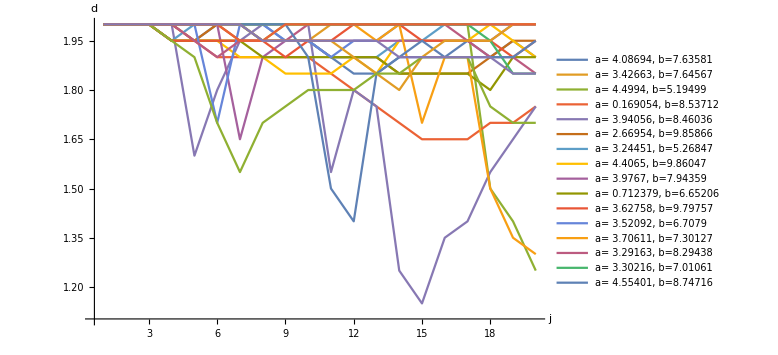

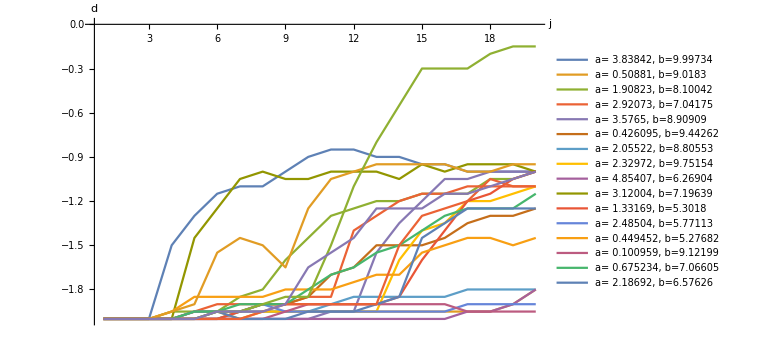

```mathematica
Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}]//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&
```

```mathematica
d
```

{-1,-2,0,1,-2,2,-2,0,1,1,0,0,0,-2,2,2,2,1,0,2}

```mathematica
d//Mean
```

1/4